```mathematica
(*Pseudorandom number generator
-We use L'Ecuyer's LCG to generate pseudorandom numbers uniformly distributed
-Then we use the Box-Muller method to obtain psuedorandom numbers distributed according to a standard Gaussian.*)

(*1) L'Ecuyer's LCG
-n is the number of terms from the sequence that we want to compute (m is too large)*)
m=2^(64);
a=3202034522624059733;
c=1;
n=100000;
LCG[a_,m_,c_,n_]:=Module[{X},
X=ConstantArray[0,n];
For[i=2,i≤ n,i++,
X[[i]]=Mod [a*X[[i-1]]+c,m]];
X]
(*normalize to obtain distribution on [0,1]*)
ULCG[a_,m_,c_,n_]:=Module[{X},
X=LCG[a,m,c,n];
For[i=1,i≤ n,i++,
X[[i]]=X[[i]]/m];
X]
```

```mathematica
Z=ULCG[a,m,c,n];
ListPlot[{Z}]
```

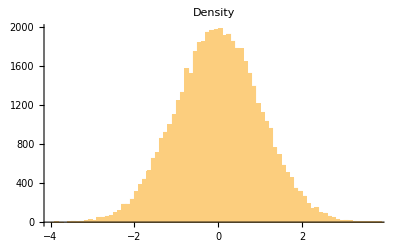

```mathematica
(*2) Box-Muller transform
-We need 2 independent uniformly distributed rvs
-Our LCG performs very well in the 2d-spectral test. Hence, we expect that if we take even/odd sequences they behave as weakly independent r.vs*)

(*Extract even/odd sequences be sure to take always n even so easy*)

U1[a_,m_,c_,n_]:=Module[{X,Y,n2,j},
n2=Floor[n/2];
X=ConstantArray[0,n2];
Y=ULCG[a,m,c,n];
j=0;
For[i=1,i≤ n2,i++,
X[[i]]=Y[[2*i-1]] ];
X]
U2[a_,m_,c_,n_]:=Module[{X,Y,n2,j},
n2=Floor[n/2];
X=ConstantArray[0,n2];
Y=ULCG[a,m,c,n];
j=0;
For[i=1,i≤ n2,i++,
X[[i]]=Y[[2*i]] ];
X]


(*Obtain now two "weakly independent" normally distributed Random variables
-Notice that since ULCG[[1]]=0 and the period is m, since we are only looking at n<<n elements it will never happen that V[[i]]=0*)
Z1[a_,m_,c_,n_]:=Module[{Z,U,V,n2},
n2=Floor[n/2];
Z=ConstantArray[0,n2];
U=U1[a,m,c,n];
V=U2[a,m,c,n];
For[i=1,i≤ n2,i++,
Z[[i]]=N[Sqrt[-2*Log[V[[i]]]]*Cos[2π*U[[i]]]] ];
Z]

Z2[a_,m_,c_,n_]:=Module[{Z,U,V,n2},
n2=Floor[n/2];
Z=ConstantArray[0,n2];
U=U1[a,m,c,n];
V=U2[a,m,c,n];
For[i=1,i≤ n2,i++,
Z[[i]]=N[Sqrt[-2*Log[V[[i]]]]*Sin[2π*U[[i]]]] ];
Z]


Z1list=Z1[a,m,c,n];
Z2list=Z2[a,m,c,n];
Show[Histogram[Z1list,100,PlotLabel->"Density"]]
```